```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\daq-tools-bkg-auto\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures\\nstar\\runs2"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/daq-tools-bkg-auto/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metadesc={Number,Number,Number,Number,Number,Number,Number,Word,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,seperator,"desctf_c.dat"],metadesc];
dimdesc=Dimensions[descdat][[1]];
rundat={};
starttime=3.7135388154693394*^9;
pta=pte=fta=fte=erra=erre={};
bpt10=bft10=errb10={};
bpt20=bft20=errb20={};
bpt0=bft0=errb0={};
pma=pme={};
pmarun=pmerun={};
pmb0run=pmbbrun={};
For[i=dimdesc/3,i≤dimdesc,i++,
pmarun=pmerun={};
pmb0run=pmbbrun={};
If[(descdat[[i]][[5]]>100&&descdat[[i]][[5]]<1000(*&&MemberQ[{1,2,3,4,5,39,40,41},i]*))
,
Print[descdat[[i]][[4]]];
rundat=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl2.dat"],{Real,Real,Real,Real,Real,Real,Real,Real,Real}];
dimrundat=Dimensions[rundat][[1]];
(*If[i==1,starttime=rundat[[1]][[1]]];
A*)
pta=Join[pta,Transpose[{(rundat[[;;,1]]-starttime)/(24*3600),rundat[[;;,{2,3}]]}]];
fta=Join[fta,Transpose[{(rundat[[;;,1]]-starttime)/(24*3600),rundat[[;;,2]]}]];
erra=Join[erra,rundat[[;;,3]]];
pma=Join[pma,Table[PlusMinus[rundat[[k]][[2]],rundat[[k]][[3]]],{k,1,dimrundat}]];
pmarun=Join[pmarun,Table[PlusMinus[rundat[[k]][[2]],rundat[[k]][[3]]],{k,1,dimrundat}]];
(*E*)
pte=Join[pte,Transpose[{(rundat[[;;,1]]-starttime)/(24*3600),rundat[[;;,{4,5}]]}]];
fte=Join[fte,Transpose[{(rundat[[;;,1]]-starttime)/(24*3600),rundat[[;;,4]]}]];
erre=Join[erre,rundat[[;;,5]]];pme=Join[pme,Table[PlusMinus[rundat[[k]][[4]],rundat[[k]][[5]]],{k,1,dimrundat}]];
pmerun=Join[pmerun,Table[PlusMinus[rundat[[k]][[4]],rundat[[k]][[5]]],{k,1,dimrundat}]];
(*B*)
If[descdat[[i]][[6]]==10,{bpt10=Join[bpt10,Transpose[{(rundat[[;;,1]]-starttime)/(24*3600),rundat[[;;,{8,9}]]}]];
bft10=Join[bft10,Transpose[{(rundat[[;;,1]]-starttime)/(24*3600),rundat[[;;,8]]}]];
errb10=Join[errb10,rundat[[;;,9]]];
pmbbrun=Join[pmbbrun,Table[PlusMinus[rundat[[k]][[8]],rundat[[k]][[9]]],{k,1,dimrundat}]];
},
{bpt20=Join[bpt20,Transpose[{(rundat[[;;,1]]-starttime)/(24*3600),rundat[[;;,{8,9}]]}]];
bft20=Join[bft20,Transpose[{(rundat[[;;,1]]-starttime)/(24*3600),rundat[[;;,8]]}]];
errb20=Join[errb20,rundat[[;;,9]]];
pmbbrun=Join[pmbbrun,Table[PlusMinus[rundat[[k]][[8]],rundat[[k]][[9]]],{k,1,dimrundat}]];
}
];
bpt0=Join[bpt0,Transpose[{(rundat[[;;,1]]-starttime)/(24*3600),rundat[[;;,{6,7}]]}]];
bft0=Join[bft0,Transpose[{(rundat[[;;,1]]-starttime)/(24*3600),rundat[[;;,6]]}]];
errb0=Join[errb0,rundat[[;;,7]]];
pmb0run=Join[pmb0run,Table[PlusMinus[rundat[[k]][[6]],rundat[[k]][[7]]],{k,1,dimrundat}]];
];
]
Print["Final ratios, A: ",Mean[pma]];
Print["Final ratios, Tau_A: ",Sqrt[(300*.1)/Mean[pma][[2]]]];
Print["Final ratios, (E-1): ",Mean[pme]];
Print["Final ratios, Tau_(E-1): ",Sqrt[(300*.1)/Mean[pme][[2]]]];
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\daq-tools-bkg-auto\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\runs2

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

13099

13142

13146

Final ratios, A: -0.0001±0.00033

Final ratios, Tau_A: 301.511

Final ratios, (E-1): -0.0013±0.0004

Final ratios, Tau_(E-1): 273.861

```mathematica
descdat[[1]][[5]]
```

189

## A

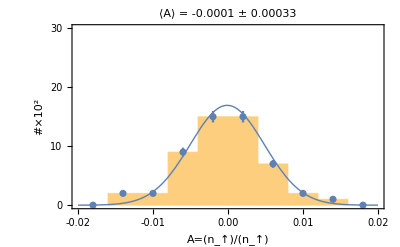

```mathematica
hista=Join[fta[[;;,2]],Table[-.004,{k,1,8}],Table[.002,{k,1,10}],Table[-.008,{k,1,5}]];
inset=Show[{
Histogram[hista,{-0.02,0.02,.004}, Frame->True,FrameLabel->{"A=(n_↑)/(n_↑)","#×10^2"},Axes->False,PlotRange->{{-.02,.02},{0,30}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->22],LabelStyle->{22,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{300},PlotLabel->"⟨A⟩ = -0.0001 ± 0.00033"],
EDAListPlot[Table[{HistogramList[hista,{-0.02,0.02,.004}][[1]][[k]]+.002,{HistogramList[hista,{-0.02,0.02,.004}][[2]][[k]],Sqrt[HistogramList[hista,{-0.02,0.02,.004}][[2]][[k]]]/4}},{k,1,Dimensions[HistogramList[hista,{-0.02,0.02,.004}][[2]]][[1]]}]],
Plot[0.21PDF[NormalDistribution[Mean[pma][[1]],Mean[pma][[2]]*15],x],{x,-0.02,0.02},PlotStyle->Thick]
},ImageSize->{400}]
```

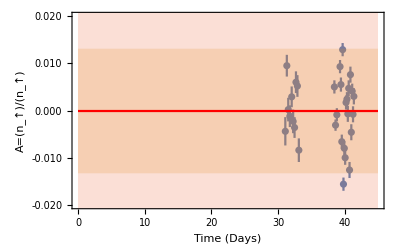

```mathematica
(***)
Show[{
EDAListPlot[pta,PlotRange->{{0,45},{-.02,0.02}},Frame->True,FrameLabel->{"Time (Days)","A=(n_↑)/(n_↑)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.002],ImageSize->{1600},Epilog->Inset[inset,{22,-.01}]],
Plot[{Mean[pma][[1]],Mean[pma][[1]]-Mean[pma][[2]]*40,Mean[pma][[1]]+Mean[pma][[2]]*40,Mean[pma][[1]]-Mean[pma][[2]]*80,Mean[pma][[1]]+Mean[pma][[2]]*80},{x,0,45},PlotStyle->{Red,None,None,None,None},Filling->{{2->{3}},{4->{5}}}]
}]
```

## E-1

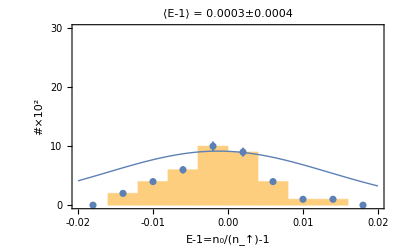

```mathematica
histe=Join[fte[[;;,2]],Table[-.004,{k,1,7}]];
inset=Show[{
Histogram[histe,{-0.02,0.02,.004}, Frame->True,FrameLabel->{"E-1=n_0/(n_↑)-1","#×10^2"},Axes->False,PlotRange->{{-.02,.02},{0,30}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->22],LabelStyle->{22,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{300},PlotLabel->"⟨E-1⟩ = 0.0003±0.0004"],
EDAListPlot[Table[{HistogramList[histe,{-0.02,0.02,.004}][[1]][[k]]+.002,{HistogramList[histe,{-0.02,0.02,.004}][[2]][[k]],Sqrt[HistogramList[histe,{-0.02,0.02,.004}][[2]][[k]]]/4}},{k,1,Dimensions[HistogramList[histe,{-0.02,0.02,.004}][[2]]][[1]]}]],
Plot[0.34PDF[NormalDistribution[Mean[pme][[1]],Mean[pme][[2]]*37],x],{x,-0.02,0.02},PlotStyle->Thick]
},ImageSize->{400}]
```

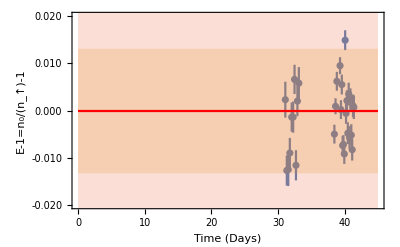

```mathematica
(***)
Show[{
EDAListPlot[pte,PlotRange->{{0,45},{-.02,0.02}},Frame->True,FrameLabel->{"Time (Days)","E-1=n_0/(n_↑)-1"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.002],ImageSize->{1600},Epilog->Inset[inset,{22,-.01}]],
Plot[{Mean[pma][[1]],Mean[pma][[1]]-Mean[pma][[2]]*40,Mean[pma][[1]]+Mean[pma][[2]]*40,Mean[pma][[1]]-Mean[pma][[2]]*80,Mean[pma][[1]]+Mean[pma][[2]]*80},{x,0,45},PlotStyle->{Red,None,None,None,None},Filling->{{2->{3}},{4->{5}}}]
}]
```

## B

```mathematica
(***)
Show[{
EDAListPlot[bpt0,bpt20,PlotRange->{{0,45},{-.001,.025}},PlotStyle->{Gray,Blue,Red},Frame->True,FrameLabel->{"Time (Days)","B (mT)"},PlotLegends->{"B_0","|B_↑,_↓|=.01 mT","|B_↑,_↓|=.02 mT"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.002],ImageSize->{1000},PlotMarkers->{Automatic,Large}]
}]
```

-Graphics-

```mathematica
bpt10
```

{}